The main idea is that ML can help figure out patterns and determine some conjectures. Also, the idea is of regularity. It figures out patterns in the data, and the existence of patterns means that maybe it is consistent i.e. there is some rule or regularity that we can exploit. For instance, in the case of latin squares, there is an iff condition that we can check whether a Latin square is a the Cayley table of a group. And it actually learns it with good enough accuracy!

Note that it would be useful to look at job applications and at least try for something. So let’s do both things. But here...ote that there isn;’t a rush. However, i gotta be very careful with the choices etc.

### Machine-Learning Mathematical Structures - Prof. Yang Hui He

Many computations were made to help resolve the 4-color theorem in 1976. And the classification of finite simple groups, which is a huge theorem, was done by Gorenstein using so much computer software. Computer software will become inevitable in doing mathematics soon.

An inspection of how mathematics has been done clearly shows that experience and experimentation precedes formalization.  To borrow again a term in theoretical physics, this approach to mathematics - of gaining insight from a panorama of results and data, combined with inspired experimentation - can be called top-down.

ML is excellent at finding patterns apparently. Well, yes, that’s what a neural net does very well. It does do the higher order classification pretty well because there are different layers which can be engineered to look at specific features of the image. Now, a neural net should be able to think about it that way. However, the amount of training data needed to do that is quite large.

We can also connect to the super computer over here.

#### Methodology

It will be interesting to see how convolutional neural networks work. Apparently, they use filters to focus on local information.  One of the important points to consider here is that there is no inherent randomness in the input-output in mathematics i.e. there is no “noise”. Like all apples are not the same size and colour but certain features stand out (compression). I guess in mathematics human use the same approach.

Support vector machines: this is a very interpretable way to analyze data by finding an optimal hyperplane (using kernel tricks etc.) which separate data-points with different labels. The hyperplane is found by maximising the distance between points with different labels.

In the classification problem, the way we measure the performance is by using the correlation probably etc. or the precision. So basically, if we have n classes, we can have a matrix M with M_ij be the number of cases predicted to be j when the actual value is i. So we minimize the sum of diagonal entries etc. compared to diagonal entries. We use both the precision and the Matthews correlation coefficient.

Is there a pattern? This could range from finding clustering

#### Exploring the Landscape of mathematics

Ok. We can read about this later.

### Conjecture formulating machine

### Learning algebraic structures

#### Intro

Indeed, can AI machine-learn calculations in algebraic geometry without understanding any mathematics but by pure pattern recognition?

But what if understanding mathematics really is just some sort of pattern recognition? Is that what the human brain really does?

I mean, AI can do something related to elliptic curves as well.

We proceed to the studying of finite groups by focusing on concrete problems:

1. Can AI recognize whether a finite group is simple just by “looking” at a Cayley table?

2. Can AI guess the number of (isomorphism classes of) subgroups to a finite groups by “looking” at the Cayley table, and

3. How good is AI at recognizing isomorphisms between finite groups.

We can isomorphic quiver representations etc. There are many things to learn here. Etc.

Definition (Matthews correlation). The Matthews correlation is defined in terms of the chi-squared of the confusion matrix as a contingency table, and explicitly, as ϕ = √(χ^2/b).

Here ϕ = 1 means perfect correlation, ϕ = 0 means randomly guessing, and ϕ = 1 means complete disagreement

Definition (Learning curve). Let {x_i -> y_i}_(i=1,..,N) be N data points. Then we take a fraction γ N of the data randomly and the remaining (1- γ)N data points for testing. Then the performance of the ML algorithm (evaluated using goodness of fit measures etc.) with respect to γ is called the learning curve L(γ).

#### Latin square -> Cayley table correspondence

A latin square is basically a n× n matrix where no row or column has a unique number. However, not every latin square is a Cayley table of some group. For instance, the identity element puts some restrictions as well.

Note that for a given size, we can computer the number of finite groups up to isomorphism. And then the number of Cayley tables is that times (n!)^2 because we can rearrange the rows and columns together.

Question. How does one efficiently recognize a random Latin square of size n to be the Cayley table of a finite group of size n?

This seems like a hard question. And obviously, there may be an algorithm to do it. However, can we show that there must exist an algorithm? Well, there doesn’t seem to be a very halting problem type problem over here, so there must be some algorithm but it might be very hard.

So the first step is data collection. We first have to create a supervised machine learning algorithm so we construct random Cayley tables up to size n and latin squares. And then we can label those latin squares 1 and the others all 0. So this is a binary classification algorithm.

This is the algorithm we use is taking a random subset of the data and split into training and test data. Then we put a classifier function that minimizes the mean square error, and we compute the rounded figure on the test data. We compute the Matthews coefficient and compute the average, std. deviation etc. Maybe we can also take k-nearest neighbours (however, it may not be suitable because the changing a Cayley table slightly will make a lot of difference).

We also want to see how performance changes as training size increases. If it doesn’t improve, that means that there may be no underlying pattern or something.

Theorem. A latin square a_ij is the Cayley multiplication of a finite group iff the quadrangle criterion holds i.e.

Now, we need to be a little careful that the ML algorithm is not just recognizing permutations but is really distinguishing true Cayley tables. Well, to do that, we just modify the training data in some way. For instance, if in hte training data, we give it all the Cayley tables it can probably figure out the “equivalence classes” under permutations. However, in the training data, we don’t give it all the groups. So there is must be some genuine property over here.

The warm-up exercise of whether given a Latin square, AI can recognize it to be the Cayley
table of a finite group was very assuring. Here, using finite groups of order 8 and 12 as test ground, we find that ML can “learn” that a Latin is truly a Cayley table to precision/accuracy more than 90%. While there is a known theorem of testing this, the standard algorithm is itself not efficient since many permutations need to be performed for the explicit check. The AI has somehow managed to do the identification without knowing anything about groups.

It should be emphasized that the AI is doing more than merely recognizing permutations.
In fact, there is no current good ML techniques [Ting] which are adapted to recognizing
random permutations. What the AI is spotting are some inherent patterns in the structure,
such as Theorem 3.2 which underlie the question of when a Latin square is a Cayley table. Now, that’s not an easy pattern. So now if that pattern will lead a continuous behaviour or something that  in the embedding. However, there is no reason that there will be a hyperplane separating these...it’s nice to think about.

#### Simple groups

Now we would like to look at the Cayley table and decide whether the group is simple or not. This looks like a very non-trivial task.

Note that we are adhering to the ATLAS notation where the elements of G are denoted as {1,2,3...,n}.  So the first few Cayley tables are given here

corresponding to the groups identity, C_2, C_3,C_4,D_4 etc. Now we also look at permutations of these which will represent the same group. So we have all the training data.

So we construct a concrete database consisting of all finite groups up to and including size 70. So the number of groups up to isomorphism is 602. So we get the Cayley tables for each group and we permute their rows and stuff to get 60000 Cayley tables and then we have labels. The labels are invariant under the permutations so somehow in the embedding, the machine learning algorithm can figure out the details as well. Then we take a random training sample of γ% etc. and then we see how it works.

With our more balanced dataset, training on 5000 random samples (less than 1/4) and validating against the remaining 3/4 gives a precision of 98.36% and with φ = 0.96. The question here is that what is the AI learning? The idea is that the trend continues...and these trends are somehow based on continuity and lack of randomness. So if there is some hyperplane separating the things, the hyperplane is talking about some sort of detail.

### p-groups

So this is the  number of groups of order n.

The question is that is there some pattern which can be figured out via ML? The idea here is that if we just give it a function, it seems random. However, there is a background context where the patterns from one step to the other are so complex that it doesn’t seem like. So it seems like a big jump. Emergent complexity. It might be worth studying this stuff over here. We can start making commits to Github nowadays to make some AI stuff here and there. So yeah. See. Things compound. So let’s start today. I also

So here the idea is that  X∈ℕ, then X can take any value in the naturals, and Y =f(X) is the number of finite groups up to isomorphism. Note that X completely determines Y, so we can try to learn the function f(X), which is what modern machine learning is about. Neural networks create functions which are continuous and approximate arbitrary functions with continuous functions (which are dense in the sup norm). However, there are many patterns which may not be continuous but still are patterns. For example, the number of prime factors of a number. Maybe it is continuous in some topology? So how to learn those things? Well, maybe the final result is some continuous process of the final thing. We can try that.

Another question is that where we can learn the distribution of Y? That seems reasonable but we know the distributio if it is f(X),

It will be nice to formalize this in terms of. So we have that there is a sequence f(n) which is apparently random i.e. we have a sequence of random variables X_1 X_2....X_n... where each X_i is uniformly distributed over the naturals. So now given that if we have information that X_i = f(Y(i)) where Y(i) is the set of all groups of order i and f is the cardinality function.

#### Zeroth

Naive approximation.

#### First try

Well, a very easy way is to use the cayley tables. So we have cayley tables plotted in some space, and the idea will be to predict where other points of the cayley table may lie. And the mebedding will somewhat highlight the order of the group.

#### Cayley graphs

We can do some unsupervised learning maybe.

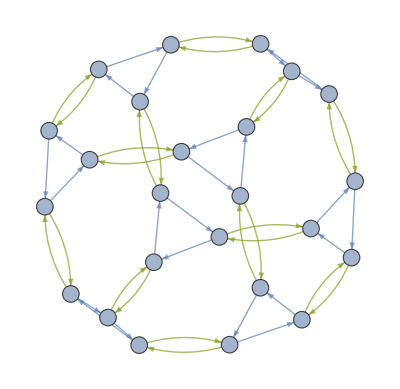

```mathematica
CayleyGraph[PermutationGroup[{Cycles[{{1,5,4}}],Cycles[{{3,4}}]}],VertexLabels->Placed["Name",Center],VertexSize->0.4]
```

```mathematica
CayleyGraph[PermutationGroup[{Cycles[{{1,2}}],Cycles[{{2,3}}],Cycles[{{3,4}}]}]]
```

-Graphics-

#### Intro

Definition (gnu(n)). This is the set of groups of order n up to isomorphism.

Definition (moa(n)). This is the minimal element of the set of numbers m for which gnu(m) = n, provided this exists.

We have all these lemma:

Definition (x^y) . If x,y∈G, then x^y denotes the conjugacy action of y on x i.e. it gives y^-1 x y.

Definition. In the free group F_r of rank r, generated by x_1,...,x_r, let N be the subgroup generated by all of the words x^(p^2), [x,y]^p, and [x,y,z] where x,y,z are just elements of the free group. 	Then G_r := F_r/N.

Note that by lemma 3.3, we get that [x^p,y] lies in N by lemma 3.3 apparently. We

Theorem. For any positive integer m and p be a prime. Then, gnu(p^m) >= p^(2/27 m^2(m-6)).

Proof.

Theorem. For any positive integer m, gnu(p^m)<= p^(2/27 m^3+ O(m^(5/2))).

So there are some interesting results.

1

References

[0]. Prelims. 
https://www.cambridge.org/core/services/aop-cambridge-core/content/view/47AFB0A2FEE8DB805FF3B953BD50CCEA/9780511542756c3_p11-22_CBO.pdf/preliminaries.pdf
[1]. Enumerating p-groups: a lower bound. https://www.cambridge.org/core/services/aop-cambridge-core/content/view/8E21D64472685CCA7DA4BE73801A024C/9780511542756c4_p23-27_CBO.pdf/enumerating_pgroups_a_lower_bound.pdf
[2]. Enumerating p-groups: upper bounds. https://www.cambridge.org/core/services/aop-cambridge-core/content/view/C6FBD5B700B8DCF5AC2BF02816BE0416/9780511542756c5_p28-44_CBO.pdf/enumerating_pgroups_upper_bounds.pdf
[3[. Enumeration of finite grups with abelian sylow subgroups.
https://www.cambridge.org/core/services/aop-cambridge-core/content/view/B32D43532113A0706CF8156A76A92A81/9780511542756c12_p102-112_CBO.pdf/enumeration_of_finite_groups_with_abelian_sylow_subgroups.pdf
[4]. Group extensions and cohomology
[5]. The orders of groups. https://www.cambridge.org/core/services/aop-cambridge-core/content/view/6027270F46E557B92C8B15463C9CEC33/9780511542756c10_p94-97_CBO.pdf/orders_of_groups.pdf
[6]. gnu, moa etc.
[7]. on the enumeration of finite groups (erdos, ram murty, kumar murty).

#### GNU, MOA etc.

The greatest values of gnu are those just mentioned, namely its values at powers of 2, which dominate the others in a quite surprising way. For example, if a group is selected at random from all the groups of order < 2048, the odds are more than 100-to-1 that it will have order 1024. The 423171191 groups of all the other orders < 2048 are swamped by the 49487365422 of order 1024. The vast majority, 48803495722, of the latter have exponent-2 class 2, and it is the fact that the number of groups of this special type can be counted without explicit construction that has enabled gnu(1024) to be precisely calculated; an algorithm to perform this calculation is described in [7].

Definitely a lot of pattern finding here. I think it will take time do a project. However, I can atleast do something over here and stuff.

#### On the enumeration of finite groups

Theorem. We know that gnu(n) <= n^(c (log n)^2) for some c > 0.

Theorem. Let n be square-free. Then G(n) <= ∏_(p|n) gcd(p-1,n).

Theorem. If n is square free, then G(n) <= φ(n).

Proof. This probably has to do with the orders of the elements. The order divides the size of the group, and so it must be one of the primes or one of the factors.  I’m

And I guess we can look at subgroups etc. Maybe we also look at the presentation or something and do something with that stuff.

Maybe we will look at the cayley tables etc. over here.

Well, let’s think about how to construct these groups. So the idea here is that we can introduce the number generators and then see which generators can lead to which groups over here. The first thing is the order of an element to figure out. And then we introduce relations.

One approach to think about is that we need to input n and the output would be the number of groups. Obviously, an input output relationship won’t help exactly. So basically we have to define what the input is. Let’s say it’s the number of generators. a

One approach is to make the ML understand what is a valid presentation or not. It seems like somewhat of a computational task. And then which of them are the same thing.

1. Number of generators. And the different possible Cayley graphs related to it. And so then we can use it to count. Let’s do this. Let’s just try this.
2. Size of the group. Output will be the different cayley graphs correspinding to that.

Basically,

Also we know that n is square free, then G(n) <= \[Curlyp

ALso when n is square free, the number of groups reduces dramatically.